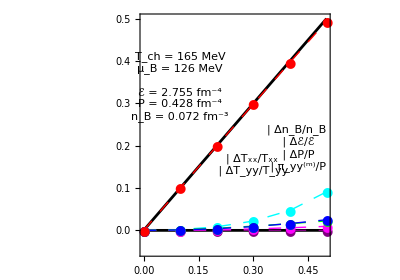

```mathematica
(* Subscript[π, xx] = - Subscript[π, yy]*)

T = 0.165;
μB =0.126; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00038037,0.0015216,0.003424,0.006088,0.0095153,0.013706,0.018661};

RPioverPdata = {0.0,0.00099992,0.004008,0.0090,0.016021,0.025054,0.036115,0.049214};

RpioverPdata =Sqrt[0.5]* {0.0,0.14135,0.2823,0.42245,0.56138,0.6987,0.834,0.96688};

ΔTxxoverTxxdata = {0.0,0.0013892,0.0049373,0.0099319,0.015867,0.022376};

ΔTyyoverTyydata = {0.0,0.0018036,0.0083568,0.022113,0.047167,0.090904};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};



legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},

{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP/P",FontSize->18,FontFamily->"Times"]},{Graphics[{Red,Disk[]},ImageSize->10],Style["π_yy^(m)/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Graphics[{RGBColor[0,1,1],Disk[]},ImageSize->10],Style["ΔT_xx/T_xx",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,1,0],Disk[]},ImageSize->10],Style["ΔT_yy/T_yy",FontSize->18,FontFamily->"Times"]}}],Background->White];



legend2=Panel[Grid[{{Style["T_ch = 165 MeV",FontSize->16,FontFamily->"Times"]},
{Style["μ_B = 126 MeV",FontSize->16,FontFamily->"Times"]},{},
{Style["ℰ = 2.755 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["P = 0.428 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["n_B = 0.072 fm^-3",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
RPioverPplot = Table[{frac[[i]],RPioverPdata[[i]]},{i,1,Length[frac]}];
RpioverPplot  = Table[{frac[[i]],RpioverPdata [[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];
ΔTyyoverTyyplot = Table[{frac[[i]],ΔTyyoverTyydata[[i]]},{i,1,Length[frac]}];

pi1=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},ImageSize->{450,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔTyyoverTyyplot,ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,RPioverPplot,RpioverPplot},PlotRange->{-0.1,1},Joined->True,ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{RGBColor[0,1,1],Thick,Dashing[Medium]},{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.418,0.194}],Inset[legend2,{0.10,0.34}],Inset[legend3,{0.295,0.155}]},ImageSize->{400,330}]
```

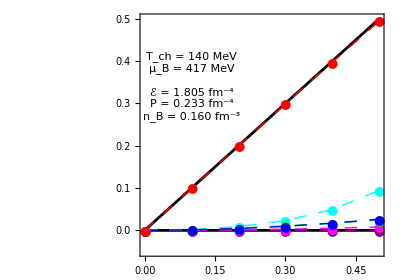

```mathematica
T = 0.140;
μB =0.417; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00031684,0.0012674,0.0028517,0.0050699,0.007922,0.011408,0.015528};

RPioverPdata = {0.0,0.0010609,0.004244,0.0095526,0.016989,0.026559,0.038268,0.052123};

RpioverPdata = Sqrt[0.5]*{0.0,0.14136,0.28234,0.42257,0.56167,0.69927,0.835,0.96848};


ΔTxxoverTxxdata = {0.0,0.0014724,0.0052523,0.010606,0.017012,0.024091};

ΔTyyoverTyydata = {0.0,0.0018982,0.0087658,0.023119,0.049156,0.094436};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};


legend2=Panel[Grid[{{Style["T_ch = 140 MeV",FontSize->16,FontFamily->"Times"]},
{Style["μ_B = 417 MeV",FontSize->16,FontFamily->"Times"]},{},
{Style["ℰ = 1.805 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["P = 0.233 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["n_B = 0.160 fm^-3",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
RPioverPplot = Table[{frac[[i]],RPioverPdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
RpioverPplot  = Table[{frac[[i]],RpioverPdata [[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];
ΔTyyoverTyyplot = Table[{frac[[i]],ΔTyyoverTyydata[[i]]},{i,1,Length[frac]}];

pi2 =Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},ImageSize->{450,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔTyyoverTyyplot,ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,RPioverPplot,RpioverPplot},PlotRange->{-0.1,1},Joined->True,ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{RGBColor[0,1,1],Thick,Dashing[Medium]},{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->Inset[legend2,{0.1,0.34}],ImageSize->{400,330}]
```

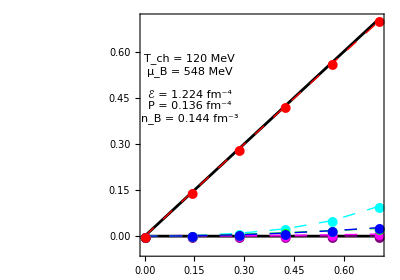

```mathematica
T = 0.120;
μB =0.548; 

frac=Table[Sqrt[2]*0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.0027367,0.0010946,0.0024628,0.0043779,0.0068398,0.0098479,0.013402};

RPioverPdata = {0.0,0.00111,0.0044464,0.010,0.017792,0.027808,0.04005,0.054538};

RpioverPdata = {0.0,0.14136,0.28237,0.42267,0.56192,0.69976,0.83584,0.96983};

ΔTxxoverTxxdata = {0.0,0.0015412,0.0055131,0.011165,0.017963,0.025517};

ΔTyyoverTyydata = {0.0,0.0019763,0.0091028,0.023947,0.05079,0.097336};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};



legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},

{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP/P",FontSize->18,FontFamily->"Times"]},{Graphics[{Red,Disk[]},ImageSize->10],Style["√2π_yy^(m)/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend2=Panel[Grid[{{Style["T_ch = 120 MeV",FontSize->16,FontFamily->"Times"]},
{Style["μ_B = 548 MeV",FontSize->16,FontFamily->"Times"]},{},
{Style["ℰ = 1.224 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["P = 0.136 fm^-4",FontSize->16,FontFamily->"Times"]},{Style["n_B = 0.144 fm^-3",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
RPioverPplot = Table[{frac[[i]],RPioverPdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
RpioverPplot  = Table[{frac[[i]],RpioverPdata [[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];
ΔTyyoverTyyplot = Table[{frac[[i]],ΔTyyoverTyydata[[i]]},{i,1,Length[frac]}];

pi3 =Show[{{
Plot[{x,0.0},{x,0,Sqrt[0.5]},PlotRange->{-0.05,Sqrt[0.5]},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔTyyoverTyyplot,ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,RPioverPplot,RpioverPplot},PlotRange->{-0.1,1},Joined->True,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{RGBColor[0,1,1],Thick,Dashing[Medium]},{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->Inset[legend2,{0.135,0.48}],ImageSize->{400,330},FrameLabel->{"(T_yy-T_xx)/2P"}]
```

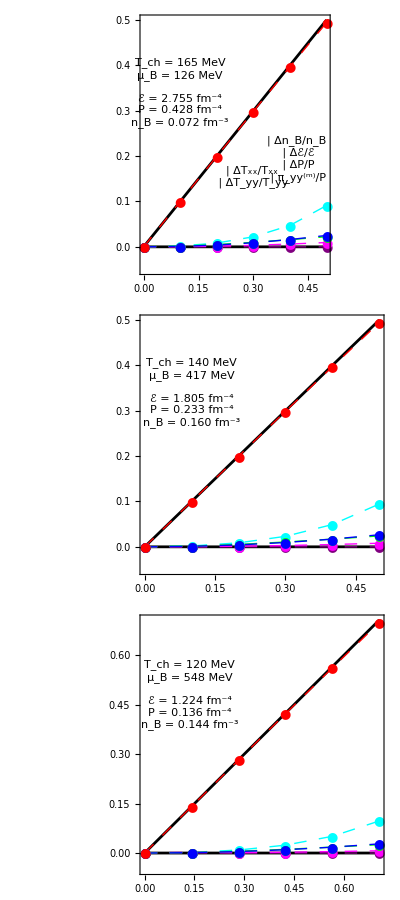

```mathematica
pitotal=Grid[{{pi1},{pi2},{pi3}}]
```